```mathematica
(*Ramil Nigmatullin 2018. *)
(* TESTING MAXENT SIS EPIDEMIC MODEL IN SMALL NETWORKS *)
(* Supplementary to "Thermodynamic efficiency of contagions: 
A statistical mechanical analysis of the SIS epidemic model",
N. Harding, R. Nigmatullin and M. Prokopenko, 2018 *)
```

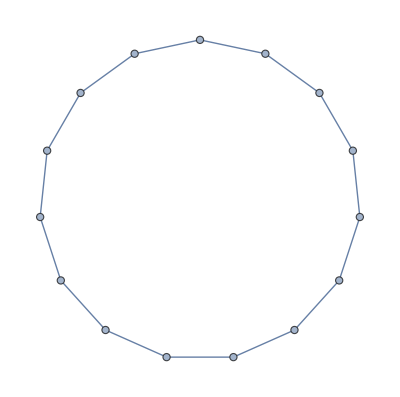
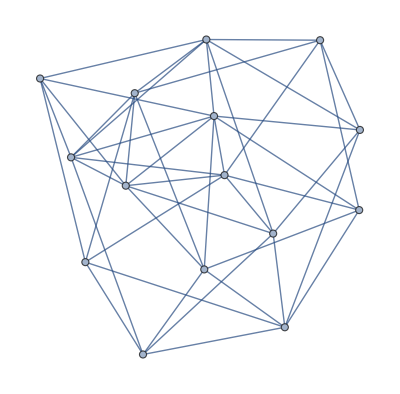
```mathematica
(* Choose one of the graph configurations - ring or a Wattz-Strogatz graph *)
(* The Wattz-Strogatz graph was generated using 
RandomGraph[WattsStrogatzGraphDistribution[15,1,3]] *)
graph="Wattz-Strogatz";

If[graph=="Ring",g=
-Graphics-;,Null];
If[graph=="Wattz-Strogatz",g=
-Graphics-;,Null];

nnodes=VertexCount[g];
```

```mathematica
(* Construct a least of neighbours for each vertex*)
adj=Normal[AdjacencyMatrix[g]];
neighbors={};

For[ww=1,ww≤nnodes,ww++,
entry={};
For[kk=1,kk≤nnodes,kk++,
If[adj[[ww]][[kk]]==1,AppendTo[entry,kk],Null];
];
AppendTo[neighbors,entry];
];
nneighbors =VertexDegree[g];
```

```mathematica
(****************************************************)
(* NUMERICALLY SIMULATE THE SIS PROCESS ON THE GRAPH*)
(****************************************************)
```

```mathematica
(* SET THE SIMULATION PARAMETERS *)
(* ν:= Transmission probability parameter *)
(* δ := Recovery probability parameter *)
(* Suggested values for the Wattz-Strogatz case ν=3.288*10^(-4) and δ=0.0005;*)
(* Suggested values for the ring case ν=0.001;  and δ=0.0006;*)

If[graph=="Ring",ν=0.001; δ=0.0006; ,Null];
If[graph=="Wattz-Strogatz",ν=3.288*10^(-4);δ=0.0005; ,Null];

NSTEPS = 120000 ;(* Number of simulation steps*)
data={}; (* Empty list for storing the results of the simulation*)

(*INITIALIZE THE SYSTEM*)
initialinfectedprobability=0.25;
state=RandomVariate[BinomialDistribution[1,initialinfectedprobability],nnodes];
statenew=state;

AppendTo[data,state];

(* THE STOCHASTIC SIS DYNAMICS SIMULATION LOOP*)
For[t=1,t≤NSTEPS,t++,
If[Mod[t,20000]==0,Print[t]];

(* THE STOCHASTIC UPDATE RULE *)
For[ww=1,ww≤nnodes,ww++,
(*Attempt infection*)
probs=RandomVariate[BinomialDistribution[1,ν],nneighbors[[ww]]];
For[kk=1,kk≤nneighbors[[ww]],kk++,
If[state[[ww]]==0,
If[probs[[kk]]==1&&state[[neighbors[[ww]][[kk]]]]==1,statenew[[ww]]=1,Null];
,Null];
];
(*Attempt recovery*)
probrecovery=RandomVariate[BinomialDistribution[1,δ]];
If[probrecovery==1,statenew[[ww]]=0,Null];
];
(*update state*)
state=statenew;
If[Total[state]==0,Break[]]; (* Stop the simulation if there are no infected nodes *)

(* RECORD DATA *)
AppendTo[data,state];
];
```

```mathematica
(* COMPUTE I AND C FROM THE DATA*)
computeC[state_]:=Module[{ww,kk,c},
c=0;
For[ww=1,ww≤Length[state],ww++,
For[kk=1,kk≤nneighbors[[ww]],kk++,
If[(state[[ww]]==1&&state[[neighbors[[ww]][[kk]]]]==0)||(state[[ww]]==0&&state[[neighbors[[ww]][[kk]]]]==1),c=c+1;Null];
];
];
c=c/2;
Return[c];
];
getCaverage[data_]:=Table[N[computeC[data[[j]]]],{j,1,Length[data]}];
getIaverage[data_]:=Table[N[Total[data[[j]]]],{j,1,Length[data]}];

(*Use only the last 100000 timesteps. The first 200000 timesteps are for equilibration*)
iSim=getIaverage[data[[20001;;120000]]]; 
cSim=getCaverage[data[[20001;;120000]]];
```

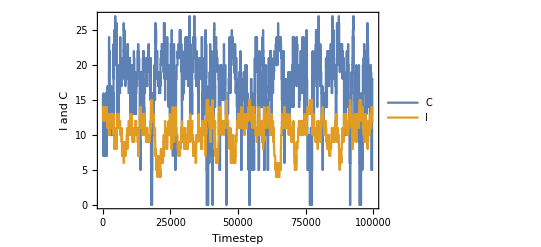

```mathematica
(* I and C as a function of time*)
ListPlot[{cSim,iSim},Joined->True,Frame->True,FrameLabel->{"Timestep","I and C"},PlotLegends->{"C","I"}]
```

```mathematica
(*Evaluate the average values of I and C denoting them by Ist and Cst *)
(* This will be used as constraints for MaxEnt model *)
Cst=Mean[cSim]
Ist=Mean[iSim]
```

16.97

10.6326

```mathematica
(*****************************************)
(* MAXENT SOLUTION *)
(*****************************************)
```

```mathematica
(* Computation of the density of state function N(I,C). *)
(* N(I,C) will be denoted by niicc *)
ii={};
cc={};
iicc={};
For[s=0,s≤2^nnodes-1,s++,
state=PadLeft[IntegerDigits[s,2],nnodes];
i=Total[state];
c=0;
For[ww=1,ww≤Length[state],ww++,
For[kk=1,kk≤nneighbors[[ww]],kk++,
If[(state[[ww]]==1&&state[[neighbors[[ww]][[kk]]]]==0)||(state[[ww]]==0&&state[[neighbors[[ww]][[kk]]]]==1),c=c+1;Null];
];
];
c=c/2;
AppendTo[ii,i];
AppendTo[cc,c];
AppendTo[iicc,{i,c}];
];
```

-Graphics3D-

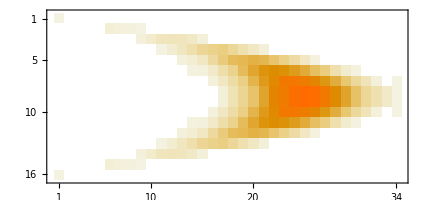

```mathematica
maxI=Max[ii];
minI=Min[ii];
maxC=Max[cc];
minC=Min[cc];
niicc=BinCounts[iicc,{minI-0.5,maxI+0.5,1},{minC-0.5,maxC+0.5,1}];

Histogram3D[iicc,AxesLabel->{"I","C","N(I,C)"},BaseStyle->Medium]
MatrixPlot[niicc]
```

```mathematica
(* CONSTRUCT THE MAXENT EQUATIONS *)
Clear[i,c,x,y,z,λ1,λ2,ψ];
exp1=0;
exp2=0;
exp3=0;

For[i=0,i≤maxI,i++,
For[c=0,c≤maxC,c++,
exp1=exp1+niicc[[i+1]][[c+1]]*i*Exp[i*λ1+c*λ2-ψ];
exp2=exp2+niicc[[i+1]][[c+1]]*c*Exp[i*λ1+c*λ2-ψ];
exp3=exp3+niicc[[i+1]][[c+1]]*Exp[i*λ1+c*λ2-ψ];
];
]

eq1=(exp1==Ist)/.{x->Exp[λ1],y->Exp[λ2]};
eq2=(exp2==Cst)/.{x->Exp[λ1],y->Exp[λ2]};
eq3=(exp3==1.0)/.{x->Exp[λ1],y->Exp[λ2]};
```

```mathematica
(* NUMERICALLY SOLVE THE MAXENT EQUATIONS*)
sol=FindRoot[{eq1,eq2,eq3},{{λ1,16.0},{λ2,3.12},{ψ,180.0}},MaxIterations->1000]
```

{λ1→0.506972,λ2→-0.164294,ψ→11.5096}

```mathematica
λ1=sol[[1]][[2]];
λ2=sol[[2]][[2]];
ψ=sol[[3]][[2]];
```

```mathematica
(* CHECK THE SOLUTION *)
exp1=0;
exp2=0;
exp3=0;
For[i=0,i≤maxI,i++,

For[c=0,c≤maxC,c++,
exp1=exp1+niicc[[i+1]][[c+1]]*i*Exp[i*λ1+c*λ2-ψ];
exp2=exp2+niicc[[i+1]][[c+1]]*c*Exp[i*λ1+c*λ2-ψ];
exp3=exp3+niicc[[i+1]][[c+1]]*Exp[i*λ1+c*λ2-ψ];
];
]
Print["Checking MaxEnt solution"]
Print[StringJoin["Exp1 = ",ToString[exp1]]];
Print[StringJoin["Exp2 = ",ToString[exp2]]];
Print[StringJoin["Exp3 = ",ToString[exp3]]];
Print[StringJoin["I^* = ",ToString[Ist]]];
Print[StringJoin["C^* = ",ToString[Cst]]];
```

Checking MaxEnt solution

Exp1 = 10.6326

Exp2 = 16.97

Exp3 = 1.

I^* = 10.6326

C^* = 16.97

```mathematica
(* GENERATE THE HYSTOGRAMS p(I), p(C) AND p(I,C) FROM THE MAXENT MODEL*)
pI={};
For[i=0,i≤maxI,i++,
temp=0.0;
For[c=0,c≤maxC,c++,
temp=temp+niicc[[i+1]][[c+1]]*Exp[i*λ1+c*λ2-ψ];
];
AppendTo[pI,{i,temp}];
];
pC={};
For[c=0,c≤maxC,c++,
temp=0.0;
For[i=0,i≤maxI,i++,
temp=temp+niicc[[i+1]][[c+1]]*Exp[i*λ1+c*λ2-ψ];
];
AppendTo[pC,{c,temp}];
];
pIC=Table[Table[0.0,{c,0,maxC}],{i,0,maxI}];
pIC={};
For[i=0,i≤maxI,i++,
For[c=0,c≤maxC,c++,
AppendTo[pIC,{i,c,niicc[[i+1]][[c+1]]*Exp[i*λ1+c*λ2-ψ]}];
];
]
```

```mathematica
(* GENERATE THE HISTOGRAMS p(I), p(C) AND p(I,C) FROM THE SIMULATION DATA*)

temp=BinCounts[cSim,{minC-0.5,maxC+0.5,1}];
SimPC=Table[{j,temp[[j+1]]},{j,0,Length[temp]-1}];
SimPC2=Table[{j,SimPC[[j+1]][[2]]/Length[cSim]},{j,0,Length[SimPC]-1}];
SimPC=SimPC2;

temp=BinCounts[iSim,{minI-0.5,maxI+0.5,1}];
SimPI=Table[{j,temp[[j+1]]},{j,0,Length[temp]-1}];
SimPI2=Table[{j,SimPI[[j+1]][[2]]/Length[iSim]},{j,0,Length[SimPI]-1}];
SimPI=SimPI2;

icSim=Table[{iSim[[j]],cSim[[j]]},{j,1,Length[iSim]}];

temp=BinCounts[icSim,{minI-0.5,maxI+0.5,1},{minC-0.5,maxC+0.5,1}];
icSim2={};
n=0;
For[i=0,i≤maxI,i++,
For[c=0,c≤maxC,c++,
AppendTo[icSim2,{i,c,temp[[i+1]][[c+1]]/Length[iSim]}];
n=n+1;
];
]
```

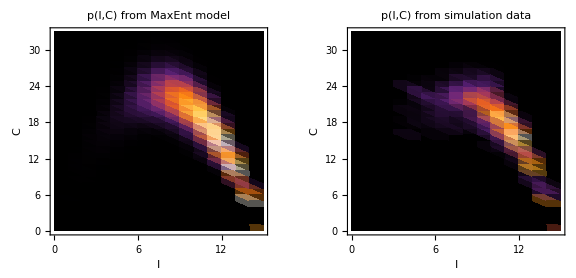

```mathematica
(* PLOT THE MAXENT AND EMPIRICAL DISTRIBUTION p(I,C) SIDE BY SIDE*)
ClearAll[pntToRect]
pntToRect[w_: 1.0]:=#/.Point->(Rectangle[{#1-w/2,0},{#1+w/2,#2}]&@@@#&)&;
pICmaxEnt=ListDensityPlot[pIC,BaseStyle->{FontSize->16},PlotRange->{{minI,maxI},{minC,maxC},{0,0.08}},ColorFunction->"SunsetColors",AspectRatio->1,FrameLabel->(Style[#,16,"Panel"]&/@{"I","C"}),PlotLabel->"p(I,C) from MaxEnt model"];
pICsim=
ListDensityPlot[icSim2,BaseStyle->{FontSize->16},PlotRange->{{minI,maxI},{minC,maxC},{0,0.08}},ColorFunction->"SunsetColors",AspectRatio->1,FrameLabel->(Style[#,16,"Panel"]&/@{"I","C"}),PlotLabel->"p(I,C) from simulation data"];
GraphicsRow[{pICmaxEnt,pICsim},ImageSize->Large]
```

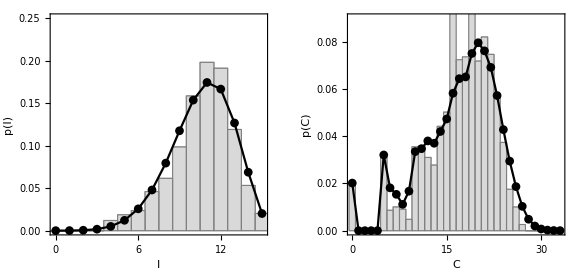

```mathematica
(* PLOT THE MAXENT AND EMPIRICAL DISTRIBUTIONS p(I) AND p(C) *)
pdata=SimPI;
minmax=Through[{Min,Max}@pdata[[All,1]]];

plI=Show[pntToRect[]@ListPlot[List/@pdata,PlotStyle->LightGray,BaseStyle->EdgeForm[Gray],PlotRange->{minmax+{-.1,.1},{0,0.25}},Frame->True,Axes->False,FrameStyle->(FontSize->14),AspectRatio->1,FrameLabel->(Style[#,16,"Panel"]&/@{"I","p(I)"})],ListPlot[pI,Joined->True,PlotMarkers->Automatic,PlotStyle->Black]];
pdata=SimPC;
minmax=Through[{Min,Max}@pdata[[All,1]]];
plC=Show[pntToRect[]@ListPlot[List/@pdata,PlotStyle->LightGray,BaseStyle->EdgeForm[Gray],PlotRange->{minmax+{-.1,.1},{0,0.09}},Frame->True,Axes->False,FrameStyle->(FontSize->14),AspectRatio->1,FrameLabel->(Style[#,16,"Panel"]&/@{"C","p(C)"})],ListPlot[pC,Joined->True,PlotMarkers->Automatic,PlotStyle->Black]];
GraphicsRow[{plI,plC},ImageSize->Large]
```